```mathematica
a=Import["~/google-gemini-pid-control-freezer/Gemini_2025-12-09_H03_M42_S12/Gemini_2025-12-09_H03_M42_S12.csv"];
```

```mathematica
a[[1]]
```

{2025 Dec 09 03:42:17.268,5.1,-16.0625,1}

```mathematica
b=Table[{a[[i,2]],a[[i,3]]},{i,Length[a]}];
```

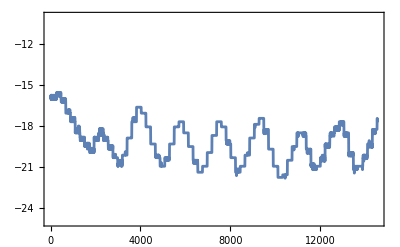

```mathematica
ListPlot[b,Joined->True,PlotRange->{-10,-25},Axes->False,Frame->True]
```